```mathematica
DSolve[g'[x] == x - 1 + g[x] x, g[x], x]
```

{{g[x]→ⅇ^(x^2/2) C[1]+ⅇ^(x^2/2) (-ⅇ^(-x^2/2)-√(π/2) Erf[x/(√2)])}}

X-√(π/2) Erfi[X/(√2)]+1/2 X^2 HypergeometricPFQ[{1,1},{3/2,2},X^2/2]

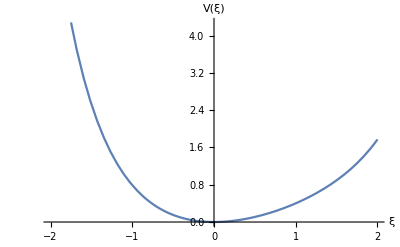

```mathematica
F = ⅇ^(x^2/2) (-ⅇ^(-x^2/2)-√(π/2) Erf[x/(√2)] + 1);
V= -Integrate[F, {x, 0, X}] //Simplify
Plot[V, {X, -2, 2},AxesLabel->{"ξ", "V(ξ)"} ]
```

```mathematica
DSolve[y'[t] == F/.{x-> y[t]}, y[t], t]
```

{{y[t]→InverseFunction[1/(2-2 ⅇ^(K[1]^2/2)+ⅇ^(K[1]^2/2) √(2 π) Erf[K[1]/(√2)])K[1]1#1&][-t/2+C[1]]}}

```mathematica
-ⅇ^(-x^2/2)-√(π/2) Erf[x/(√2)] /.{x -> 0}
```

-1